```mathematica
(*This version uses the energy functional method and try to also use the second derivative. InvertBlockedHessian changed in this version*)
Clear["Global`*"]
```

```mathematica
messageHandler=If[Last[#],Abort[]]&
Internal`AddHandler["Message",messageHandler]
```

If[Last[#1],Abort[]]&

```mathematica
linearsearch[mode_,varType_,mu_,nu_,lambda_,T0Expanded_,L0_,X1_,SL0_,S1_,quench_,reversequench_,Overlap_,OverlapExpanded_,OverlapHalfExpanded_,OverlapExpandedInv_,R0downExpanded_,R0downHalfExpanded_,H1_,ZeroExpanded_,quenchBlockD_,GroupsAOs_,GroupsMOs_,connect_,ssguess_,NMaxIterLS_,lserrortarget_,spinfactor_,epsExponent_]:=Module[{ss,sstrial,Xloc,Tloc,DMloc,Enloc,Gloc,lserror,iterls,appr2der,siginvloc,conv,g1D,g1D1,EnHistory,Detloc,DetHistory,Gsignprev,Gsign,g1D0,precision,Population,PopHistory,datatemp,eps0,plotarray,N1,En0,Penalty,ObjFunction,OF0,OFHistory,PenaltyQDev,PQDHistory,L0loc,GL0loc},


N1=Total[GroupsAOs];
precision=10;
eps0=10^-6;
conv=0;
ss=0.0;
sstrial=0.0;
Xloc=X1+ss S1;
L0loc=L0;
If[varType==3,
L0loc=L0+ss SL0;
];
EnHistory={};
DetHistory={};
OFHistory={};
PopHistory={};
PQDHistory={};
(*Print["S=",S1//MatrixForm];*)
Do[

Xloc=Xloc+sstrial S1;
If[varType==3,
L0loc=L0loc+sstrial SL0;
];

(*compute MO coefficients*)
Tloc=x2mos[varType,T0Expanded,L0loc,Xloc,Overlap,OverlapExpanded,OverlapExpandedInv,R0downExpanded,GroupsAOs,GroupsMOs,connect];

(*auxiliary matrices*)
siginvloc=Inverse[Transpose[Tloc].Overlap.Tloc];
DMloc=Tloc.siginvloc.Transpose[Tloc];

(*objective function and its key components*)
{ObjFunction,Enloc,Detloc,PenaltyQDev}=objFunction[nu,mu,lambda,Tloc,DMloc,H1,Overlap,siginvloc,reversequench,spinfactor];
If[iterls==0,
En0=Enloc;
];
EnHistory=Append[EnHistory,{ss,Enloc-En0}];
DetHistory=Append[DetHistory,{ss,Detloc}];
PQDHistory=Append[PQDHistory,{ss,PenaltyQDev}];
If[iterls==0,
OF0=ObjFunction;
];
OFHistory=Append[OFHistory,{ss,ObjFunction-OF0}];

(*collect population data*)
Population=GetPopulation[Tloc,Overlap,siginvloc,GroupsAOs,GroupsMOs];
datatemp={};
Do[
datatemp=Append[datatemp,{Table[ss,{iao,1,Length[GroupsAOs]}],eps0+Transpose[Population][[imo]]}];
,{imo,1,Length[GroupsMOs]}];
PopHistory=Append[PopHistory,datatemp];
(*end population data*)

(*grad*)
Gloc=OFGradient[varType,nu,mu,lambda,Tloc,DMloc,H1,Overlap,siginvloc,quench,reversequench,spinfactor,Xloc,L0loc,T0Expanded,OverlapExpanded,OverlapHalfExpanded,ZeroExpanded,OverlapExpandedInv,R0downExpanded,R0downHalfExpanded,quenchBlockD,GroupsAOs,GroupsMOs,connect,25,epsExponent,False];
If[varType==3,
GL0loc=OFGradient[varType+1,nu,mu,lambda,Tloc,DMloc,H1,Overlap,siginvloc,quench,reversequench,spinfactor,Xloc,L0loc,T0Expanded,OverlapExpanded,OverlapHalfExpanded,ZeroExpanded,OverlapExpandedInv,R0downExpanded,R0downHalfExpanded,quenchBlockD,GroupsAOs,GroupsMOs,connect,25,epsExponent,False];
];

(* 1D grad *)
g1D=Tr[Transpose[Gloc].S1];
If[varType==3,
g1D+=Tr[Transpose[GL0loc].SL0];
];
If[iterls==0,
g1D0=g1D;
];
(*Print["g1D=",g1D];*)
lserror=g1D/g1D0;
(*lserror=g1D/Sqrt[   Tr[Transpose[Gloc].Gloc]   Tr[Transpose[S1].S1]    ];*)
(*Print["lserror=",lserror];*)
(*If[NMaxIterLS<100,
PrintInfoLS[iterls,Enloc,g1D,lserror,sstrial,ss,precision];
];*)

(*to make decision - choose between modes*)
Switch[mode,
0,
(*scan mode*)
sstrial=(Quotient[iterls,2]+1)ssguess;
sstrial=(iterls+1)ssguess;
If[Mod[iterls,2]≠0,sstrial=-sstrial];
,
1,
(* appr. second derivative min mode*)
If[Abs[lserror]<lserrortarget,
conv=1;
PrintInfoLS[iterls,Enloc,g1D,lserror,sstrial,ss,precision];
Break[];
];
If[iterls==0,
(*iteration is zero*)
g1D1=g1D;
sstrial=ssguess
,
(*iteration is not zero*)
appr2der=(g1D-g1D1)/sstrial;
sstrial=-g1D/appr2der;
g1D1=g1D;
];
,
2 ,
(* bisection min mode*)
If[Abs[lserror]<lserrortarget,
conv=1;
PrintInfoLS[iterls,Enloc,g1D,lserror,sstrial,ss,precision];
Break[];
];
If[iterls==0,
(*iteration is zero*)
Gsignprev=Sign[g1D];
sstrial=ssguess;
,
(*iteration is not zero*)
Gsignprev=Gsign;
];
Gsign=Sign[g1D];
If[Gsignprev≠Gsign,
sstrial=-sstrial/2.0,
sstrial=sstrial*1.5
];
];(*end switch mode*)
ss=ss+sstrial;

,{iterls,0,NMaxIterLS}];
(*finish iterations*)

(*print graphs*)
(*Print[ListPlot[EnHistory]];
Print[ListLogPlot[DetHistory]];*)
(*Print[ListLogPlot[PQDHistory]];*)
(*Print[ListPlot[OFHistory]];*)
If[mode==0,
PopHistory=Transpose[PopHistory,{3,1,4,2}];
Do[
plotarray={ListLogPlot[PopHistory[[imo]]],ListPlot[PopHistory[[imo]]]};
Print[plotarray];
,{imo,1,Length[GroupsMOs]}];
];
(*end print graphs*)

If[mode≠0&&conv==0,
Print["Linear search is not converged after ",NMaxIterLS," steps. Grad norm along the step is: ",lserror];
Abort[];
];
Return[ss];

]

(*change Qproj0 after debug*)
newlinearsearch[mode_,varType_,mu_,nu_,tau_,GroupNeighbors_,lambda_,T0Expanded_,L0_,X1_,SL0_,S1_,quench_,reversequench_,Overlap_,OverlapExpanded_,OverlapHalfExpanded_,OverlapExpandedInv_,R0downExpanded_,R0downHalfExpanded_,H1_,ZeroExpanded_,quenchBlockD_,GroupsAOs_,GroupsMOs_,connect_,ssguess_,NMaxIterLS_,lserrortarget_,spinfactor_,epsExponent_]:=Module[{ss,sstrial,Xloc,Tloc,DMloc,Gloc,lserror,iterls,appr2der,conv,g1D,g1D1,EnHistory,Detloc,DetHistory,Gsignprev,Gsign,g1D0,precision,Population,PopHistory,datatemp,eps0,plotarray,N1,En0,Penalty,ObjFunction,OF0,OFHistory,PenaltyQDev,PQDHistory,L0loc,GL0loc,dgrad1,dgrad2,Qproj,Tbar},


N1=Total[GroupsAOs];
precision=10;
eps0=10^-6;
conv=0;
ss=0.0;
sstrial=0.0;
Xloc=X1+ss S1;
L0loc=L0;
If[varType==3,
L0loc=L0+ss SL0;
];
EnHistory={};
DetHistory={};
OFHistory={};
PopHistory={};
PQDHistory={};
(*Print["S=",S1//MatrixForm];*)
Do[

Xloc=Xloc+sstrial S1;

(*objective function and its key components*)
(*be sure to change after debug*)
{ObjFunction,dgrad1,dgrad2,Qproj,Tbar}=newEnergy[tau,Xloc, H1, connect,GroupsMOs,Overlap, GroupNeighbors, spinfactor,quench,1];
(*{ObjFunction,dgrad1}=newEnergyQ0[Xloc,H1,connect,GroupsMOs,Overlap,GroupNeighbors,spinfactor,quench,Qproj0];*)
If[iterls==0,
En0=ObjFunction;
];

If[iterls==0,
OF0=ObjFunction;
];
OFHistory=Append[OFHistory,{ss,ObjFunction-OF0}];

(*grad*)
(*be sure to change after debug *)
Gloc=dgrad1+dgrad2;
(*Gloc = dgrad1;*)


(* 1D grad *)
g1D=Tr[Transpose[Gloc].S1];

If[iterls==0,
g1D0=g1D;
];
(*Print["g1D=",g1D];*)
lserror=g1D/g1D0;
(*lserror=g1D/Sqrt[   Tr[Transpose[Gloc].Gloc]   Tr[Transpose[S1].S1]    ];*)
(*Print["lserror=",lserror];*)
(*If[NMaxIterLS<100,
PrintInfoLS[iterls,ObjFunction,g1D,lserror,sstrial,ss,precision];
];*)

(*to make decision - choose between modes*)
Switch[mode,
0,
(*scan mode*)
sstrial=(Quotient[iterls,2]+1)ssguess;
sstrial=(iterls+1)ssguess;
If[Mod[iterls,2]≠0,sstrial=-sstrial];
,
1,
(* appr. second derivative min mode*)
If[Abs[lserror]<lserrortarget,
conv=1;
PrintInfoLS[iterls,ObjFunction,g1D,lserror,sstrial,ss,precision];
Break[];
];
If[iterls==0,
(*iteration is zero*)
g1D1=g1D;
sstrial=ssguess
,
(*iteration is not zero*)
appr2der=(g1D-g1D1)/sstrial;
sstrial=-g1D/appr2der;
g1D1=g1D;
];
,
2 ,
(* bisection min mode*)
If[Abs[lserror]<lserrortarget,
conv=1;
PrintInfoLS[iterls,ObjFunction,g1D,lserror,sstrial,ss,precision];
Break[];
];
If[iterls==0,
(*iteration is zero*)
Gsignprev=Sign[g1D];
sstrial=ssguess;
,
(*iteration is not zero*)
Gsignprev=Gsign;
];
Gsign=Sign[g1D];
If[Gsignprev≠Gsign,
sstrial=-sstrial/2.0,
sstrial=sstrial*1.5
];
];(*end switch mode*)
ss=ss+sstrial;

,{iterls,0,NMaxIterLS}];
(*finish iterations*)

(*print graphs*)
Print[ListPlot[EnHistory]];
(*Print[ListLogPlot[DetHistory]];*)
(*Print[ListLogPlot[PQDHistory]];*)
(*Print[ListPlot[OFHistory]];*)

(*end print graphs*)

If[mode≠0&&conv==0,
Print["Linear search is not converged after ",NMaxIterLS," steps. Grad norm along the step is: ",lserror];
Abort[];
];
Return[ss];

]
getHessian[varType_,nu_,mu_,Svv_,Fvv_,Soo_,Foo_,Svo_,Fvo_,ST0_,GroupsMOs_,connect_,O1_,spinfactor_]:=Module[
{GiantHess0,GiantHessPenalty,GH,nDomains,iorbOffset,jorbOffset,iAOOff,jAOOff,inAOs,inMOs,jnAOs,jnMOs,STi,STj,SooIJ,FooIJ,SvvIJ,FvvIJ,nRows},

Switch[varType,
1,
GiantHess0=Table[1,{i,1,O1},{j,1,O1}];
Do[
Do[
GiantHess0[[iorb,jorb]]=Soo[[iorb,jorb]]Fvv[[connect[[iorb]],connect[[jorb]]]]
-Foo[[iorb,jorb]]Svv[[connect[[iorb]],connect[[jorb]]]];
(*-Transpose[{Fvo[[connect[[iorb]],jorb]]}].{Svo[[connect[[jorb]],iorb]]}
-Transpose[{Svo[[connect[[iorb]],jorb]]}].{Fvo[[connect[[jorb]],iorb]]};*)
,{jorb,1,O1}];
,{iorb,1,O1}];
GiantHess0*=nu 2.0spinfactor ;
,
2,
nDomains=Length[GroupsMOs];
iorbOffset=0;
nRows=0;
(*nCols=0*)
Do[
nRows+=Length[connect[[iorbOffset+1]]];
(*nCols+=GroupsMOs[[idomain]];*)
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];

GiantHess0=Table[1,{i,1,nRows},{j,1,nRows}];
GiantHessPenalty=Table[1,{i,1,nRows},{j,1,nRows}];

iorbOffset=0;
iAOOff=0;
(*iMOOff=0;*)
Do[
inAOs=Length[connect[[iorbOffset+1]]];
inMOs=GroupsMOs[[idomain]];
STi=ST0[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+inMOs ]];

jorbOffset=0;
jAOOff=0;
(*jMOOff=0;*)
Do[
jnAOs=Length[connect[[jorbOffset+1]]];
jnMOs=GroupsMOs[[jdomain]];
STj=ST0[[connect[[jorbOffset+1]],jorbOffset+1;;jorbOffset+jnMOs ]];

SooIJ=STi.Soo[[iorbOffset+1;;iorbOffset+inMOs , jorbOffset+1;;jorbOffset+jnMOs ]].Transpose[STj];
FooIJ=STi.Foo[[iorbOffset+1;;iorbOffset+inMOs , jorbOffset+1;;jorbOffset+jnMOs ]].Transpose[STj];
FvvIJ=Fvv[[connect[[iorbOffset+1]],connect[[jorbOffset+1]]]];
SvvIJ=Svv[[connect[[iorbOffset+1]],connect[[jorbOffset+1]]]];

Do[
Do[
GiantHess0[[iAOOff+iao,jAOOff+jao]]=(SooIJ[[iao,jao]]FvvIJ-Transpose[{SooIJ[[All,jao]]}].{FvvIJ[[iao,All]]}-Transpose[{FvvIJ[[All,jao]]}].{SooIJ[[iao,All]]}+SooIJ FvvIJ[[iao,jao]])-(FooIJ[[iao,jao]]SvvIJ-Transpose[{FooIJ[[All,jao]]}].{SvvIJ[[iao,All]]}-Transpose[{SvvIJ[[All,jao]]}].{FooIJ[[iao,All]]}+FooIJ SvvIJ[[iao,jao]]);

If [mu≠0.0,
GiantHessPenalty[[iAOOff+iao,jAOOff+jao]]=SooIJ[[iao,jao]]SvvIJ-Transpose[{SooIJ[[All,jao]]}].{SvvIJ[[iao,All]]}-Transpose[{SvvIJ[[All,jao]]}].{SooIJ[[iao,All]]}+SooIJ SvvIJ[[iao,jao]];
];
,{jao,1,jnAOs}];
,{iao,1,inAOs}];

(*jMOOff+=jnMOs;*)
jAOOff+=jnAOs;
jorbOffset+=GroupsMOs[[jdomain]];
,{jdomain,1,nDomains}];

(*iMOOff+=inMOs;*)
iAOOff+=inAOs;
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];

If [mu≠0.0,
GiantHess0=nu 2.0spinfactor GiantHess0 + mu 2.0 GiantHessPenalty;
,
GiantHess0*=nu 2.0spinfactor ;
];

];

GH=ArrayFlatten[GiantHess0];
Return[GH];

]

getBlockHessian[varType_,nu_,mu_,Svv_,Fvv_,Soo_,Foo_,Svo_,Fvo_,ST0_,GroupsMOs_,connect_,O1_,spinfactor_]:=Module[
{GiantHess0,GiantHessPenalty,nDomains,iorbOffset,iAOOff,inAOs,inMOs,STi,SooIJ,FooIJ,SvvIJ,FvvIJ,nRows},

nDomains=Length[GroupsMOs];

Switch[varType,
1,
GiantHess0=Table[1,{i,1,nDomains}];
iorbOffset=0;
Do[
GiantHess0[[idomain]]=Fvv[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]]
+Svv[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];
GiantHess0*=nu 2.0spinfactor ;
,
2,
iorbOffset=0;
GiantHess0={};
Do[
nRows=Length[connect[[iorbOffset+1]]];
GiantHess0=Append[GiantHess0,Table[1,{i,1,nRows},{j,1,nRows}]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];

(*GiantHessPenalty=Table[1,{i,1,nRows},{j,1,nRows}];*)

iorbOffset=0;
iAOOff=0;
(*iMOOff=0;*)
Do[
inAOs=Length[connect[[iorbOffset+1]]];
inMOs=GroupsMOs[[idomain]];
STi=ST0[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+inMOs ]];

SooIJ=STi.Soo[[iorbOffset+1;;iorbOffset+inMOs , iorbOffset+1;;iorbOffset+inMOs ]].Transpose[STi];
FooIJ=STi.Foo[[iorbOffset+1;;iorbOffset+inMOs , iorbOffset+1;;iorbOffset+inMOs ]].Transpose[STi];
FvvIJ=Fvv[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]];
SvvIJ=Svv[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]];

Do[
Do[
GiantHess0[[idomain,iAOOff+iao,iAOOff+jao]]=(SooIJ[[iao,jao]]FvvIJ-Transpose[{SooIJ[[All,jao]]}].{FvvIJ[[iao,All]]}-Transpose[{FvvIJ[[All,jao]]}].{SooIJ[[iao,All]]}+SooIJ FvvIJ[[iao,jao]])-(FooIJ[[iao,jao]]SvvIJ-Transpose[{FooIJ[[All,jao]]}].{SvvIJ[[iao,All]]}-Transpose[{SvvIJ[[All,jao]]}].{FooIJ[[iao,All]]}+FooIJ SvvIJ[[iao,jao]]);
(*
If [mu≠0.0,
GiantHessPenalty[[iAOOff+iao,iAOOff+jao]]=SooIJ[[iao,jao]]SvvIJ-Transpose[{SooIJ[[All,jao]]}].{SvvIJ[[iao,All]]}-Transpose[{SvvIJ[[All,jao]]}].{SooIJ[[iao,All]]}+SooIJ SvvIJ[[iao,jao]];
];
*)
,{jao,1,inAOs}];
,{iao,1,inAOs}];

(*iMOOff+=inMOs;*)
iAOOff+=inAOs;
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];

(*
If [mu≠0.0,
GiantHess0=nu 2.0spinfactor GiantHess0 + mu 2.0 GiantHessPenalty;
,*)
GiantHess0*=nu 2.0spinfactor ;
(*];*)

];

Return[GiantHess0];

]

invertBlockHessian[varType_,tau_,Hess_,GroupsMOs_, Overlap_, connect_]:=Module[
{HessDomain,HessL,HessV,RevHessL,ModHess,HessInv,shift,nDomains,iorbOffset,HessLDomains,delta,tt},
tt=0.0001;
nDomains=Length[GroupsMOs];

HessInv={};
HessLDomains={};

Do[
iorbOffset = 0;
Switch[varType,
1,
(*sdomaininvhalf=MatrixPower[Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]],-1/2];*)
HessDomain=Hess[[idomain]];
,
2,
HessDomain=ArrayFlatten[Hess[[idomain]] ];
];

{HessL,HessV}=Eigensystem[HessDomain];
(*Print[Max[Abs[HessDomain-Transpose[HessV].DiagonalMatrix[HessL].HessV]]];*)

(*Print["Domain ",idomain," eigenvalues"];
Print[ListLogPlot[Reverse[Abs[Re[HessL]]]]];*)
HessLDomains=Append[HessLDomains,HessL];

(*Modify Hessian to make it SPD*)
shift=Max[0.0,Abs[tau]-Min[Re[HessL]]];(*from Nocedal*)

ModHess=HessDomain+shift IdentityMatrix[Length[HessDomain]];
(*invert Hessian*)
(*HessInv=Append[HessInv,Inverse[ModHess]];*)

(*DANGER!!! Remove when done playing. Also uncommend the append above. *)
RevHessL=Reverse[HessL];

HessL=Reverse[RevHessL];
delta = DiagonalMatrix[Table[If[Abs[Re[HessL[[i]]]]>tt,1./HessL[[i]],0],{i,1,Length[HessDomain]}]];
HessInv=Append[HessInv,Transpose[HessV].delta.HessV];
iorbOffset += GroupsMOs[[idomain]];
,{idomain,1,nDomains}
];

Print[ListLogPlot[HessLDomains,PlotRange->All]];
Return[HessInv];


]

projectHession[varType_,taup_,Hess_,GroupsMOs_,GroupsAOs_, Overlap_, connect_,MOs_]:=Module[
{HessDomain,HessL,HessV,theta,HessInv,threshold,nDomains,iorbOffset,HessLDomains,Sdomaininvhalf,HessPInv,delta,HessProj, nNbMOs,igmo, iconnect,Hd,V,sigmaV,rhoV,Tproj,Sdomain,p1,p2,Ncutoff,ptotal},
nDomains=Length[GroupsMOs];
HessProj={};
HessPInv = {};
HessLDomains={};
iorbOffset = 0;
Do[
Switch[varType,
1,
Sdomaininvhalf=MatrixPower[Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]],-1/2];
HessDomain=Sdomaininvhalf.Hess[[idomain]].Sdomaininvhalf;

,
2,
HessDomain=ArrayFlatten[Hess[[idomain]]];
];
nNbMOs = 0;
igmo = 1;
iconnect = 1;
Do[
(*Print["iconnect ",iconnect," igmo ", igmo, " and ",GroupsAOs[[jdomain]], " and ", connect[[iorbOffset+1,iconnect]], " and ", GroupsMOs[[jdomain]]];*)
If[iconnect>Length[connect[[iorbOffset+1]]],Break[]];
If[connect[[iorbOffset+1,iconnect]]>igmo,
igmo+=GroupsAOs[[jdomain]]
,
nNbMOs += GroupsMOs[[jdomain]];iconnect+=GroupsAOs[[jdomain]];igmo+=GroupsAOs[[jdomain]];];

,{jdomain,1,nDomains}
];
{HessL,HessV}=Eigensystem[HessDomain];

threshold =Min[ Abs[Re[Reverse[HessL][[nNbMOs]]]],taup];
(*threshold = Abs[Re[Reverse[HessL][[nNbMOs]]]];*)
HessLDomains=Append[HessLDomains,HessL];

Print["domain # ",idomain," nNbMOs ", nNbMOs, "threshold ", threshold];
(*Print[ListLogPlot[Reverse[Abs[Re[HessL]]]]];*)
Ncutoff = 0;
Do[
If[Reverse[Abs[Re[HessL]]][[kk]]> threshold,Ncutoff=kk-1;Break[]];
,{kk,1,Length[HessL]}
];
Print["cutoff: ", Ncutoff];
theta = DiagonalMatrix[Table[If[Abs[Re[HessL[[i]]]]>threshold,1,0],{i,1,Length[HessDomain]}]];
delta = DiagonalMatrix[Table[If[Abs[Re[HessL[[i]]]]>threshold,1./HessL[[i]],0],{i,1,Length[HessDomain]}]];
HessProj=Append[HessProj,Inverse[Sdomaininvhalf].Transpose[HessV].theta.HessV.Sdomaininvhalf];
HessPInv=Append[HessPInv,Sdomaininvhalf.Transpose[HessV].delta.HessV.Sdomaininvhalf];
Hd = Length[HessDomain[[1]]];
V= Sdomaininvhalf.Transpose[HessV][[1;;Hd,Hd-Ncutoff+1;;Hd]];
Sdomain = Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]];
sigmaV = Transpose[V].Sdomain.V;

(*Print["Trace of rho: ",Tr[V.Inverse[sigmaV].Transpose[V].Sdomain]];*)

rhoV = Sdomain.V.Inverse[sigmaV].Transpose[V].Sdomain;
Tproj = {};
ptotal = 0.;
Do[
p1 = MOs[[connect[[iorbOffset+1]],iMO]].rhoV.MOs[[connect[[iorbOffset+1]],iMO]]/(MOs[[1;;Length[MOs],iMO]].Overlap.MOs[[1;;Length[MOs],iMO]]);
ptotal = ptotal + p1;
p2 = MOs[[connect[[iorbOffset+1]],iMO]].Sdomain.MOs[[connect[[iorbOffset+1]],iMO]]/(MOs[[1;;Length[MOs],iMO]].Overlap.MOs[[1;;Length[MOs],iMO]]);
Tproj = Append[Tproj,{p1,p2,p1-p2}];
,{iMO,1,Length[MOs[[1]]]}
];
Print["total p: ", ptotal];
Print[MatrixForm[Tproj]];
iorbOffset += GroupsMOs[[idomain]];
,{idomain,1,nDomains}
];

Return[{HessProj,HessPInv}];

]

applyBlockHessian[varType_,grad_,HessInv_,GroupsMOs_,connect_,O1_]:=Module[
{nDomains,iorbOffset,nAOs,nMOs,rowOff,Step,GradVec,StepVec},

nDomains=Length[GroupsMOs];

Switch[varType,
1,
Step=Table[0.0,{i,1,N1},{j,1,O1}];
iorbOffset=0;
Do[
nMOs=GroupsMOs[[idomain]];
Step[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+nMOs]]=-HessInv[[idomain]].grad[[ connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+nMOs]];
iorbOffset+=nMOs;
,{idomain,1,nDomains}];
,
2,
Step=grad; (*init step, all zeros are in place because the grad has the same structure*)
iorbOffset=0;
rowOff=0;
Do[
nAOs=Length[connect[[iorbOffset+1]]];
nMOs=GroupsMOs[[idomain]];
GradVec=Table[1,{i,1,nAOs},{j,1,1}];
Do[
(*row is selected as a matrix, why not column?*)
GradVec[[iao,1]]=Transpose[{grad[[rowOff+1;;rowOff+nAOs,rowOff+iao]]}];
,{iao,1,nAOs}
];
StepVec=-HessInv[[idomain]].ArrayFlatten[GradVec];
Step[[rowOff+1;;rowOff+nAOs,rowOff+1;;rowOff+nAOs]]=Transpose[Partition[  StepVec[[1;;nAOs*nAOs,1]]  ,nAOs]];
rowOff+=nAOs;
iorbOffset+=nMOs;
,{idomain,1,nDomains}];
];

Return[Step];


]

matVO2vector[varType_,matVO_,GroupsMOs_,connect_,O1_]:=Module[
{GiantVec,GV,nDomains,iorbOffset,nRows,iAOOff,inAOs,inMOs},

Switch[varType,
1,
GiantVec=Table[1,{i,1,O1},{j,1,1}];
Do[
GiantVec[[iorb,1]]=Transpose[{matVO[[connect[[iorb]],iorb]]}];
,{iorb,1,O1}
];
,
2,
(*create GiantVec*)
nDomains=Length[GroupsMOs];
iorbOffset=0;
nRows=0;
Do[
nRows+=Length[connect[[iorbOffset+1]]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];
GiantVec=Table[1,{i,1,nRows},{j,1,1}];
(*fill in GiantVec*)
iorbOffset=0;
iAOOff=0;
Do[
inAOs=Length[connect[[iorbOffset+1]]];
inMOs=GroupsMOs[[idomain]];
Do[
(*row is selected as a matrix, why not column?*)
GiantVec[[iAOOff+iao,1]]=Transpose[{matVO[[iAOOff+1;;iAOOff+inAOs,iAOOff+iao]]}];
,{iao,1,inAOs}];
iAOOff+=inAOs;
iorbOffset+=inMOs;
,{idomain,1,nDomains}];
];
GV= ArrayFlatten[GiantVec];
Return[GV];
]

vector2matVO[varType_,vector_,GroupsMOs_,connect_,N1_,O1_]:=Module[
{matVO,truevec,starti,endi,lengthi,temp,nDomains,iorbOffset,nRows,rowOff,nAOs,rowOff2},

Switch[varType,
1,
matVO=Table[0.0,{i,1,N1},{j,1,O1}];
truevec=Transpose[vector][[1]];
starti=1;
Do[
lengthi=Length[connect[[iorb]]];
endi=starti+lengthi-1;
temp=truevec[[starti;;endi]];
starti=starti+lengthi;
Do[
matVO[[connect[[iorb,ielem]],iorb]]=temp[[ielem]];
,{ielem,1,lengthi}
];
,{iorb,1,O1}
];
,
2,
nDomains=Length[GroupsMOs];
iorbOffset=0;
nRows=0;
Do[
nRows+=Length[connect[[iorbOffset+1]]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];

matVO=Table[0.0,{i,1,nRows},{j,1,nRows}];
iorbOffset=0;
rowOff=0;
rowOff2=0;
Do[
nAOs=Length[connect[[iorbOffset+1]]];
(*Do[
Do[
Atemp=Ain[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]];
Aout[[rowOff+ii,rowOff+jj]]=Atemp[[ii,jj]];
,{jj,1,nAOs}];
,{ii,1,nAOs}];*)
matVO[[rowOff+1;;rowOff+nAOs,rowOff+1;;rowOff+nAOs]]=Transpose[Partition[  vector[[rowOff2+1;;rowOff2+nAOs*nAOs,1]]  ,nAOs]];
rowOff+=nAOs;
rowOff2+=nAOs*nAOs;
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];

];
Return[matVO];
]

grad2step[varType_,projHess_, taup_,nu_,mu_,Grad_,tau_,KS_,Overlap_,T_,T0_,Proj_,siginv_,GroupsMOs_, GroupsAOs_, connect_,N1_,O1_,spinfactor_,useNewMethod_,Qproj_]:=Module[
{Fvv,Svv,Soo,Foo,Svo,Fvo,Hess,HessL,GradVec,StepVec,ModHess,Step,shift,ST0,hessStructureType,hessMatrixType,HessInv,HessPinv,HessProj,newHess,iorbOffset,nDomains},

hessStructureType=2; (* 1 - full Hessian, 2 - blocked Hessian *)
hessMatrixType=1; (* 1 - "exact", 2 - only S-matrix *)
HessProj = {};

If[hessStructureType==1 && projHess≠ 0, Print["Hessian projection can't be done for full Hession"]; Abort[]];

(*get Hessian components*)
Switch[hessMatrixType,
1,(*exact*)
Fvv=(IdentityMatrix[N1]-Overlap.Proj).KS.(IdentityMatrix[N1]-Proj.Overlap);
Svv=Overlap-Overlap.Proj.Overlap;
Foo=siginv.Transpose[T].KS.T.siginv;
Soo=siginv;
Fvo=(IdentityMatrix[N1]-Overlap.Proj).KS.T.siginv;
Svo=Overlap.T.siginv;
ST0=Overlap.T0;
,
2,(*S only*)
Fvv=IdentityMatrix[N1];
Svv=Overlap;
Foo=IdentityMatrix[O1];
Soo=IdentityMatrix[O1]; 
Fvo=Table[0.0,{i,1,N1},{j,1,O1}];
Svo=Table[0.0,{i,1,N1},{j,1,O1}];
ST0=Overlap.T0;
];

(*compute Hessian*)
Switch[hessStructureType,
1,(* full hessian *)
Hess=Chop[getHessian[varType,nu,mu,Svv,Fvv,Soo,Foo,Svo,Fvo,ST0,GroupsMOs,connect,O1,spinfactor]];
(*Print["Hess size = ",Length[Hess]];*)
(*Print[MatrixForm[Chop[Hess]]];*)
HessL=Eigenvalues[Hess];
Print[ListPlot[Reverse[Re[HessL]]]];
(*Print[MatrixForm[Chop[HessL]]];*)
(*Modify Hessian to make it SPD*)
shift=Max[0.0,Abs[tau]-Min[Re[HessL]]];(*from Nocedal*)
ModHess=Hess+shift IdentityMatrix[Length[Hess]];
(*HessL=Eigenvalues[ModHess];Print[MatrixForm[HessL]];*)
(*apply Hessian*)
GradVec=matVO2vector[varType,Grad,GroupsMOs,connect,O1];
(*Print[MatrixForm[Chop[GradVec]]];*)
StepVec=-Inverse[ModHess].GradVec;
Step=vector2matVO[varType,StepVec,GroupsMOs,connect,N1,O1];
,
2,(*blocked hessian*)
Print["Blocked Hessian"];
Hess=Chop[getBlockHessian[varType,nu,mu,Svv,Fvv,Soo,Foo,Svo,Fvo,ST0,GroupsMOs,connect,O1,spinfactor]];
If[projHess≠0,
{HessProj,HessPinv}= projectHession[varType,taup,Hess,GroupsMOs, GroupsAOs, Overlap, connect,T];
Step=applyBlockHessian[varType,Grad,HessPinv,GroupsMOs,connect,O1];
,
If[useNewMethod==0,
HessInv=invertBlockHessian[varType,tau,Hess,GroupsMOs, Overlap, connect];
Step=applyBlockHessian[varType,Grad,HessInv,GroupsMOs,connect,O1];
,
newHess = Hess;
nDomains= Length[GroupsMOs];
iorbOffset=0;
(*new hessian*)
Do[

newHess[[idomain]] = Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]].Qproj[[idomain]].Hess[[idomain]].Transpose[Qproj[[idomain]]].Transpose[Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];
HessInv=invertBlockHessian[varType,tau,newHess,GroupsMOs, Overlap, connect];
Step=applyBlockHessian[varType,Grad,HessInv,GroupsMOs,connect,O1];
];

]

];

Return[{Step,HessProj}];


]

Gnormalized[Xraw_,G_,Overlap_,appropriateQuench_]:=Module[
{normalizer,SXraw,Graw},
normalizer=MatrixPower[DiagonalMatrix[Diagonal[Transpose[Xraw].Overlap.Xraw]],-1/2];
SXraw=appropriateQuench(Overlap.Xraw);
Graw=G.normalizer-SXraw.MatrixPower[normalizer,3].DiagonalMatrix[Diagonal[Transpose[G].Xraw]];
Return[Graw];

]

dOFdT2dOFdX[varType_,dEdT_,X_,L0_,T0Expanded_,Overlap_,OverlapExpanded_,OverlapHalfExpanded_,ZeroExpanded_,OverlapExpandedInv_,R0downExpanded_,R0downHalfExpanded_,quench_,quenchBlockD_,GroupsAOs_,GroupsMOs_,connect_,nMaxSteps_,eps_]:=Module[
{Delta,G,dEdTexpanded,TG,Mul,factorial,CurrPower,TGpos,CurrTerm,Gadd,GaddNorm,converged,XExpanded,C1matrix,C2matrix,siginvL0},

(*N1=Length[Overlap];*)
Switch[varType,
1,
G=dEdT;
,
2,
converged==0;
(*Sexpanded=expandMatrix["AO-AO",Overlap,GroupsMOs,connect];*)
Delta=X-Transpose[X];(*X is in the expanded form*)
Delta=Delta.OverlapExpanded;
(*Texpanded=expandMatrix["AO-MO",T0,GroupsMOs,connect];*)
dEdTexpanded=expandMatrix["AO-MO",dEdT,GroupsMOs,connect];
TG=T0Expanded.Transpose[dEdTexpanded];
(*M0=Table[0.0,{i,1,N1},{j,1,N1}];
M0expanded=expandMatrix["AO-AO",M0,GroupsMOs,connect];*)
G=ZeroExpanded;
factorial=1;
Do[
CurrPower=ZeroExpanded;
TGpos=1;
Do[
CurrTerm=ZeroExpanded;
Do[
If[k==TGpos,
Mul=TG,
Mul=Delta
];
If[k==1,
CurrTerm=Mul,
CurrTerm=CurrTerm.Mul
];
,{k,1,i}
];
CurrPower+=CurrTerm;
TGpos++;
,{j,1,i}
];
factorial*=i;
Gadd=OverlapExpanded.CurrPower/factorial;
GaddNorm=Max[Abs[Gadd]];
G+=Gadd;
If[GaddNorm<eps,
(*Print["exponent converged, iter=",i];*)
converged==1;
Break[]
];
,{i,1,nMaxSteps}
];
G=-(G-Transpose[G]);
If[converged==0,Print["Gradient series is not converged"];Abort[]];
,
3,(* X part of the T = L0.norm + (I-R0).X.norm *)
dEdTexpanded=expandMatrix["AO-MO",dEdT,GroupsMOs,connect];
dEdTexpanded=dEdTexpanded-R0downExpanded.OverlapExpandedInv.dEdTexpanded;
G=collapseMatrix[dEdTexpanded,GroupsAOs,GroupsMOs,connect];
G=Gnormalized[X,G,Overlap,quench];
,
4, (* L0 part of the T = L0.norm + (I-R0).X.norm *)
siginvL0=Inverse[Transpose[L0].Overlap.L0];
dEdTexpanded=expandMatrix["AO-MO",dEdT,GroupsMOs,connect];
XExpanded=expandMatrix["AO-MO",X,GroupsMOs,connect];
C1matrix=Transpose[OverlapHalfExpanded-R0downHalfExpanded].XExpanded.Transpose[dEdTexpanded].OverlapExpandedInv.OverlapHalfExpanded;
C2matrix=Transpose[OverlapHalfExpanded].XExpanded.Transpose[dEdTexpanded].OverlapExpandedInv.(OverlapHalfExpanded-R0downHalfExpanded);
G=quenchBlockD (dEdT-C1matrix.L0.siginvL0-Transpose[C2matrix].L0.siginvL0);
G=Gnormalized[L0,G,Overlap,quenchBlockD];
];

Return[G];

]

x2mos[varType_,T0Expanded_,L0_,X_,Overlap_,OverlapExpanded_,OverlapExpandedInv_,R0downExpanded_,GroupsAOs_,GroupsMOs_,connect_]:=Module[
{Delta,MOs,Texpanded,XExpanded,Xpart,sigmaD},

Switch[varType,
1,
MOs=X;
,
2,
(*Sexpanded=expandMatrix["AO-AO",Overlap,GroupsMOs,connect];*)
Delta=(X-Transpose[X]).OverlapExpanded;
(*T0expanded=expandMatrix["AO-MO",T0,GroupsMOs,connect];*)
Texpanded=MatrixExp[Delta].T0Expanded;
MOs=collapseMatrix[Texpanded,GroupsAOs,GroupsMOs,connect];
,
3,
sigmaD=DiagonalMatrix[Diagonal[Transpose[X].Overlap.X]];
Xpart=X.MatrixPower[sigmaD,-1/2];
XExpanded=expandMatrix["AO-MO",Xpart,GroupsMOs,connect];
XExpanded=XExpanded-OverlapExpandedInv.R0downExpanded.XExpanded;
Xpart=collapseMatrix[XExpanded,GroupsAOs,GroupsMOs,connect];
sigmaD=DiagonalMatrix[Diagonal[Transpose[L0].Overlap.L0]];
MOs=Xpart+L0.MatrixPower[sigmaD,-1/2];
,
4,
Print["DO NOT CALL x2mos with varType 4 !!!"];
Abort[];
];

Return[MOs];

]

objFunction[nu_,mu_,lambda_,MOs_,Proj_,H1_,Overlap_,siginv_,reversequench_,spinfactor_]:=Module[
{Energy,NormalizedMOs,SigmaDet,PenaltyDet,qTdeviation,PenaltyQDev,ObjFunction},

Energy=spinfactor Tr[Proj.H1];
NormalizedMOs=MOs.MatrixPower[DiagonalMatrix[Diagonal[Transpose[MOs].Overlap.MOs]], -1/2];
SigmaDet=Det[Transpose[NormalizedMOs].Overlap.NormalizedMOs];
PenaltyDet=-mu Log[SigmaDet];
qTdeviation=reversequench NormalizedMOs;
PenaltyQDev=lambda Tr[Transpose[qTdeviation].Overlap.qTdeviation];
ObjFunction=nu Energy+PenaltyDet+PenaltyQDev; 

Return[{ObjFunction,Energy,SigmaDet,PenaltyQDev}];

]

(*---------------------------------------------------------------------------------------------------------------------------------------------------------------dasdf*)
newEnergy[tau_,MOs_,H1_,connect_,GroupsMOs_,Overlap_,GroupNeighbors_,spinfactor_,quench_,doGrad_]:=Module[
{NormalizedMOs,newMOs,newRho,Ebar,sigmabar,ndomain,iorbOffset,minidx,maxidx,outside,
delta,Qproj,Tpartial,sigmaxy,Tnb,Tnbdomain,GradT,siginv,N1,NMO,signific,Tsigmabar,Kmatrix,Grady,deltaE,newGrad1,newGrad2},
ndomain=Length[GroupsMOs];
NormalizedMOs=MOs.MatrixPower[DiagonalMatrix[Diagonal[Transpose[MOs].Overlap.MOs]],-1/2];
iorbOffset=0;
newMOs=MOs;
Ebar=0.;
deltaE = 0.;
N1=Length[Overlap];
NMO = Length[MOs[[1]]];
siginv = Inverse[Transpose[MOs].Overlap.MOs];
Qproj = {};
signific = {}; (*store for each MO, the domains it's significant on*)
Tsigmabar = {};
Tnbdomain = {};(* Us this to pick out a specific MO x in Tsigmabar*)
newGrad1 = {};
newGrad2 = {};

Do[
signific = Append[signific,{}];
,{iMO,1,NMO}
];

Do[
(*find problematic MOs*)
Tnb={};

Do[
minidx=1;
maxidx=1;
Do[
minidx+=GroupsMOs[[nidomain]];
,{nidomain,1,GroupNeighbors[[idomain,inb]]-1}
];
maxidx=minidx+GroupsMOs[[GroupNeighbors[[idomain,inb]]]]-1;

outside=nolap[connect,iorbOffset+1,minidx];
Do[delta=0.;
If[Length[outside]>0,
Southalf = MatrixPower[Overlap[[outside,outside]],1/2];
outabs=Southalf.NormalizedMOs[[outside,nbidx]];
For[ii=1,ii≤Length[outside],ii++,delta+=outabs[[ii]]outabs[[ii]];];
];


If[delta<tau,Tnb=Append[Tnb,nbidx];
(*cuffMO = Table[0,{i,1,N1}];
cuffMO[[outside]]=MOs[[outside,nbidx]];
W = Append[W,cuffMO];*)
signific[[nbidx]]= Append[signific[[nbidx]],idomain];
];
,{nbidx,minidx,maxidx}
];(*each MO in neighbor domains*),
{inb,1,Length[GroupNeighbors[[idomain]]]}
];(*For each neighbor domain*)

Tpartial=MOs[[connect[[iorbOffset+1]],Tnb]];
Tnbdomain = Append[Tnbdomain,Tnb];
If[Length[Tnb]>0,
sigmaxy=Transpose[Tpartial].Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]].Tpartial;

newMOs[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]]=
(IdentityMatrix[Length[connect[[iorbOffset+1]]]]-Tpartial.Inverse[sigmaxy].Transpose[Tpartial].
Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]]).
MOs[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]];

(*Print["Q on this domain"];
Print[MatrixForm[Tpartial.Inverse[Qsigma].Transpose[Tpartial]]];
Print["And the new modified MO"];
Print[MatrixForm[newMOs[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]]]]; *)

(*Tfull = MOs[[Overlap[[1;;Length[Overlap]]],Tnb]];
sigmafull = Transpose[Tfull].Overlap.Tfull;
Qfull = Tfull.sigmafull.Transpose[Tfull];
KK= (IdentityMatrix[N1]-Qfull.Overlap).Transpose[W].Inverse[sigmafull].Transpose[MOs];
deltaE += Tr[(KK+Transpose[KK]).Overlap.MOs.Transpose[GradT]]; *)
];
If[Length[Tnb]>0,
Qproj = Append[Qproj,(Inverse[Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]]]
-Tpartial.Inverse[sigmaxy].Transpose[Tpartial])];
Tsigmabar = Append[Tsigmabar,Tpartial.Inverse[sigmaxy]];
,
Qproj = Append[Qproj,Inverse[Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]]]];
Tsigmabar = Append[Tsigmabar,{}];
];

iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,ndomain}
];

sigmabar=Transpose[newMOs].Overlap.newMOs;
newRho=newMOs.Inverse[sigmabar].Transpose[newMOs];
Ebar=spinfactor Tr[newRho.H1];

(*calculate the gradient*)
If[doGrad≠0,
GradT=2.0 spinfactor quench(IdentityMatrix[N1]-Overlap.newRho).H1.newMOs.Inverse[sigmabar];

newGrad1 = GradT;
newGrad2 = Table[0.,{i,1,N1},{j,1,NMO}];
iorbOffset = 0;
Do[
newGrad1[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]]=
Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]].Qproj[[idomain]].
GradT[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,Length[GroupsMOs]}
];

(*This part is for newGrad2*)
Do[
If[Length[signific[[iMO]]]>0,
For[ii=1,ii≤ Length[signific[[iMO]]],ii++,
minidx = 1;
maxidx = 1;
For[jj=1,jj<signific[[iMO,ii]],jj++,minidx += GroupsMOs[[jj]];];
maxidx = minidx + GroupsMOs[[signific[[iMO,ii]]]]-1;
Kmatrix = GradT[[connect[[minidx]],minidx;;maxidx]].Transpose[MOs[[connect[[minidx]],minidx;;maxidx]]].Overlap[[connect[[minidx]],connect[[minidx]]]];
Kmatrix = Kmatrix + Transpose[Kmatrix];
Grady = -(Overlap[[connect[[minidx]],connect[[minidx]]]].Qproj[[signific[[iMO,ii]]]]).Kmatrix.Tsigmabar[[signific[[iMO,ii]]]];
(*pick out iMO in Tsigmabar*)
MOtest = 0;
For[kk=1,kk≤ Length[Tnbdomain[[signific[[iMO,ii]]]]],kk++,
If[Tnbdomain[[signific[[iMO,ii]],kk]]==iMO,
MOtest = 1; newGrad2[[connect[[minidx]],iMO]]+= Grady[[1;;Length[connect[[minidx]]],kk]];Break;
];
];
If[MOtest == 0, Print["!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!MO test error!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!"]];
];
]
,{iMO,1,NMO}
];

newGrad2 = quench newGrad2;
];(*End if dograd*)
(*Print[MatrixForm[newGrad1]];
Print[MatrixForm[newGrad2]];*)
Return[{Ebar,newGrad1,newGrad2,Qproj,newMOs}];
]


(*-------------------seperate routine just for new energy with constant(input) Q ----------------------------------------------*)
newEnergyQ0[MOs_,H1_,connect_,GroupsMOs_,Overlap_,GroupNeighbors_,spinfactor_,quench_,Q0_]:=Module[
{NormalizedMOs,newMOs,newRho,Ebar,sigmabar,ndomain,iorbOffset,GradT,siginv,N1,NMO,signific,deltaE,newGrad1},
ndomain=Length[GroupsMOs];
NormalizedMOs=MOs.MatrixPower[DiagonalMatrix[Diagonal[Transpose[MOs].Overlap.MOs]],-1/2];
iorbOffset=0;
newMOs=MOs;
Ebar=0.;
deltaE = 0.;
N1=Length[Overlap];
NMO = Length[MOs[[1]]];
siginv = Inverse[Transpose[MOs].Overlap.MOs];
newGrad1 = {};

Do[
newMOs[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]]=
Q0[[idomain]].Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]].
MOs[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,ndomain}
];

sigmabar=Transpose[newMOs].Overlap.newMOs;
newRho=newMOs.Inverse[sigmabar].Transpose[newMOs];
Ebar=spinfactor Tr[newRho.H1];

(*calculate the gradient*)
GradT=2.0 spinfactor quench(IdentityMatrix[N1]-Overlap.newRho).H1.newMOs.Inverse[sigmabar];

newGrad1 = GradT;
iorbOffset = 0;
Do[
newGrad1[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]]=
Overlap[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]].Q0[[idomain]].
GradT[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]]]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,Length[GroupsMOs]}
];

(*Print[MatrixForm[newGrad1]];
Print[MatrixForm[newGrad2]];*)
Return[{Ebar,newGrad1}];
]


nolap[connect_,iMO_,inMO_]:=Module[
{list,idx1,idx2},
list={};
idx1=1;
idx2=1;
While[idx1≤Length[connect[[iMO]]]&&idx2≤Length[connect[[inMO]]],If[connect[[iMO,idx1]]>connect[[inMO,idx2]],list=Append[list,connect[[inMO,idx2]]];idx2++;,If[connect[[iMO,idx1]]<connect[[inMO,idx2]],idx1++;,If[connect[[iMO,idx1]]==connect[[inMO,idx2]],idx1++;
idx2++;];];];];
If[idx2≤Length[connect[[inMO]]],
For[jj=idx2,jj≤Length[connect[[inMO]]],jj++,list=Append[list,connect[[inMO,jj]]];];
];
list
]

OFGradient[varType_,nu_,mu_,lambda_,MOs_,Proj_,H1_,Overlap_,siginv_,quench_,reversequench_,spinfactor_,X_,L0_,T0Expanded_,OverlapExpanded_,OverlapHalfExpanded_,ZeroExpanded_,OverlapExpandedInv_,R0downExpanded_,R0downHalfExpanded_,quenchBlockD_,GroupsAOs_,GroupsMOs_,connect_,nStepsExponent_,epsExponent_,doNumG_]:=Module[
{N1,GradEwrtT,GradQTpenwrtT,GradDetPenaltywrtT,GradOFwrtT,Gfinal,NormalizedMOs,qTdeviation,appropriateQuench},

NormalizedMOs=MOs.MatrixPower[DiagonalMatrix[Diagonal[Transpose[MOs].Overlap.MOs]], -1/2];
N1=Length[Overlap];

qTdeviation=reversequench NormalizedMOs;
GradEwrtT=2.0 spinfactor(IdentityMatrix[N1]-Overlap.Proj).H1.MOs.siginv;
GradQTpenwrtT=2.0 lambda reversequench Overlap.qTdeviation;
GradDetPenaltywrtT=-2.0 mu Overlap.MOs.siginv;
GradOFwrtT= quench (nu GradEwrtT+GradDetPenaltywrtT)+GradQTpenwrtT;
Gfinal=dOFdT2dOFdX[varType,GradOFwrtT,X,L0,T0Expanded,Overlap,OverlapExpanded,OverlapHalfExpanded,ZeroExpanded,OverlapExpandedInv,R0downExpanded,R0downHalfExpanded,quench,quenchBlockD,GroupsAOs,GroupsMOs,connect,nStepsExponent,epsExponent];

(* compare to numerical gradient *)
If[doNumG,
If[varType==4,
appropriateQuench=quenchBlockD;
,
appropriateQuench=quench;
];
getNumGrad[Gfinal,varType,nu,mu,lambda,X,L0,appropriateQuench,H1,Overlap,OverlapExpanded,OverlapExpandedInv,spinfactor,0.0001,4,reversequench,connect,GroupsAOs,GroupsMOs];
];

Return[Gfinal];

]

(*expand AO-indices into block-diagonal matrices*)
expandMatrix[type_,Ain_,GroupsMOs_,connect_]:=Module[
{A0,Aout,nDomains,iorbOffset,jorbOffset,nRows,nCols,rowOff,colOff,nAOs,nMOs,Atemp,nColsOriginal},

nDomains=Length[GroupsMOs];

(* old code relies on pretty unreliable ArrayFlatten*)
(*
A0=Table[1,{i,1,nDomains},{j,1,nDomains}];
iorbOffset=0;
Do[
jorbOffset=0;
Do[
Switch[type
,
"AO-AO",
A0[[idomain,jdomain]]=KroneckerDelta [idomain,jdomain]Ain[[connect[[iorbOffset+1]],connect[[jorbOffset+1]]]];
,
"AO-MO",
A0[[idomain,jdomain]]=KroneckerDelta [idomain,jdomain]Ain[[connect[[iorbOffset+1]],jorbOffset+1;;jorbOffset+GroupsMOs[[jdomain]] ]];
];
jorbOffset+=GroupsMOs[[jdomain]];
,{jdomain,1,nDomains}];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];
Aout= ArrayFlatten[A0];
*)

iorbOffset=0;
nRows=0;
nCols=0;
Do[
nRows+=Length[connect[[iorbOffset+1]]];
nCols+=GroupsMOs[[idomain]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];

nColsOriginal=Length[Ain[[1]]];

Switch[type
,
"AO-AO",
Aout=Table[0.0,{i,1,nRows},{j,1,nRows}];
iorbOffset=0;
rowOff=0;
Do[
nAOs=Length[connect[[iorbOffset+1]]];
Aout[[rowOff+1;;rowOff+nAOs,rowOff+1;;rowOff+nAOs]]=Ain[[connect[[iorbOffset+1]],connect[[iorbOffset+1]]]];
rowOff+=nAOs;
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];
,
"AO-keep",
Aout=Table[0.0,{i,1,nRows},{j,1,nColsOriginal}];
iorbOffset=0;
rowOff=0;
Do[
nAOs=Length[connect[[iorbOffset+1]]];
Aout[[rowOff+1;;rowOff+nAOs,All]]=Ain[[connect[[iorbOffset+1]],All]];
rowOff+=nAOs;
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];
,
"AO-MO",
Aout=Table[0.0,{i,1,nRows},{j,1,nCols}];
iorbOffset=0;
rowOff=0;
colOff=0;
Do[
nAOs=Length[connect[[iorbOffset+1]]];
nMOs=GroupsMOs[[idomain]];
Aout[[rowOff+1;;rowOff+nAOs,colOff+1;;colOff+nMOs]]=Ain[[  connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+nMOs ]];
colOff+=nMOs;
rowOff+=nAOs;
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}];
];


Return[Aout];

]

(* collapse expanded AO-indices into matrix *)
collapseMatrix[Ain_,GroupsAOs_,GroupsMOs_,connect_]:=Module[
{matVO,nDomains,iorbOffset,O1,N1,starti,lengthi,endi,temp},

nDomains=Length[GroupsMOs];
N1=Total[GroupsAOs];
O1=Total[GroupsMOs];
matVO=Table[0.0,{i,1,N1},{j,1,O1}];
iorbOffset=0;
starti=1;
Do[
lengthi=Length[connect[[iorbOffset+1]]];
endi=starti+lengthi-1;
temp=Ain[[starti;;endi,iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]] ]];
starti=starti+lengthi;
Do[
matVO[[connect[[iorbOffset+1,ielem]],iorbOffset+1;;iorbOffset+GroupsMOs[[idomain]] ]]=temp[[ielem,1;;GroupsMOs[[idomain]] ]];
,{ielem,1,lengthi}
];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}
];
Return[matVO];

]

PrintInfo[label_,iter_,Energy_,Det_,QDev_,ObjFun_,Gnorm_,stepsize_,precision_]:=Module[
{},
Print[label," Iter=",iter,", Stepsize=",NumberForm[stepsize,precision],", Energy=",NumberForm[Energy,precision],", Det=",NumberForm[Det,precision],", QDev=",NumberForm[QDev,precision],", ObjF=",NumberForm[ObjFun,precision],", GNorm=",NumberForm[Gnorm,precision]];
]

PrintInfoLS[iter_,Energy_,Gnorm_,Grel_,steptrial_,stepac_,precision_]:=Module[
{},
Print[" LS it = ",iter,", E = ",NumberForm[Energy,precision+3],", Tr[G.S] = ",NumberForm[Gnorm,precision],", Rel.error = ",NumberForm[Grel,precision],", Trial step = ", NumberForm[steptrial,precision], ", Accumulated step = ",NumberForm[stepac,precision]];
]

GetPopulation[T1_,Overlap_,siginv_,GroupsAOs_,GroupsMOs_]:=Module[
{A1,M1,off1,off2},
A1=T1 (Overlap.T1.siginv);
M1=Table[0.0,{i,1,Length[GroupsAOs]},{j,1,Length[GroupsMOs]}];
off2=0;
Do[
off1=0;
Do[
M1[[i,j]]=Sum[A1[[k,m]],{k,off1+1,off1+GroupsAOs[[i]]},{m,off2+1,off2+GroupsMOs[[j]]}];
off1=off1+GroupsAOs[[i]];
,{i,1,Length[GroupsAOs]}];
off2=off2+GroupsMOs[[j]];
,{j,1,Length[GroupsMOs]}];
Return[M1];
]

characterizeMOs[T_,Overlap_,H1_,quench_,revquench_,spinfactor_]:=Module[{xT,sigma,SigmaDet,Energy,siginv,Proj,GradEwrtT,GradEwrtTq,GradNorm,rqT,qDev,qGradNorm,TNorm},

TNorm=Tr[Transpose[T].Overlap.T];
xT=T.MatrixPower[DiagonalMatrix[Diagonal[Transpose[T].Overlap.T]], -1/2];
sigma=Transpose[xT].Overlap.xT;
SigmaDet=Det[sigma];
siginv=Inverse[sigma];
Proj= xT.siginv.Transpose[xT];
Energy=spinfactor Tr[Proj.H1];
GradEwrtT=2.0 spinfactor(IdentityMatrix[N1]-Overlap.Proj).H1.xT.siginv;
GradEwrtTq=GradEwrtT quench;
GradNorm=Max[Abs[GradEwrtT]];
qGradNorm=Max[Abs[GradEwrtTq]];
rqT=revquench xT;
qDev=Tr[Transpose[rqT].Overlap.rqT];
Print["|T|=",NumberForm[TNorm,16],", E=",NumberForm[Energy,16],", Det=",NumberForm[SigmaDet,16],", |G|=",NumberForm[GradNorm,16],", |q G|=",NumberForm[qGradNorm,16],", |rq T_n|=",NumberForm[qDev,16]];

]

getNumGrad[Ganalytical_,varType_,nu_,mu_,lambda_,X_,L0_,appropriateQuench_,H1_,Overlap_,OverlapExpanded_,OverlapExpandedInv_,spinfactor_,delta0_,nDeltas_,reversequench_,connect_,GroupsAOs_,GroupsMOs_]:=Module[
{nCols,nRows,delta,GnumPos,GnumNeg,imo,iao,iX,iL0,siginv,MOs,Proj,En,OF,OFZero,DeltaOF,GZeroNorm,Gnpdiff,GnpdiffNorm,Gnumdiff,GnumdiffNorm,GnumPosNorm,GnumNegNorm,R0down,R0downExpanded,iDOFincluded,T0Expanded,SigmaDet,PenaltyQDev},

T0Expanded={}; (* set to empty because varType==2 is not implemented anyway*)
If[varType==1||varType==3||varType==4,
Print["Numerical gradient varType = ",varType];
nCols=Total[GroupsMOs];
nRows=Total[GroupsAOs];
,
Print["Numerical gradient varType = ",varType, " NOT DEFINED"];
Return[];
];

(* if varType≠4, L0 can be updated outside the loop *)
If[varType==3,
R0down= Overlap.L0.Inverse[Transpose[L0].Overlap.L0].Transpose[L0].Overlap;
R0downExpanded=expandMatrix["AO-AO",R0down,GroupsMOs,connect];
];

(*loop over delta values*)
delta=delta0;
Do[

GnumPos=Table[0.0,{i,1,nRows},{j,1,nCols}];
GnumNeg=Table[0.0,{i,1,nRows},{j,1,nCols}];
(* loop over DOFs *)
Do[

imo=Quotient[iDOF-1,nRows]+1;
iao=Mod[iDOF-1,nRows]+1;

iDOFincluded=0;
If[iDOF==0,iDOFincluded=1];
If[iDOF≠0,
If[appropriateQuench[[iao,imo]]≠0,iDOFincluded=1];
];

If[iDOFincluded==1,
Do[

If[varType==4,
iL0=L0;
If[iDOF≠0,
iL0[[iao,imo]]+=isign delta;
];
R0down= Overlap.iL0.Inverse[Transpose[iL0].Overlap.iL0].Transpose[iL0].Overlap;
R0downExpanded=expandMatrix["AO-AO",R0down,GroupsMOs,connect];
MOs=x2mos[3,T0Expanded,iL0,X,Overlap,OverlapExpanded,OverlapExpandedInv,R0downExpanded,GroupsAOs,GroupsMOs,connect];
,
iX=X;
If[iDOF≠0,
iX[[iao,imo]]+=isign delta;
];
MOs=x2mos[varType,T0Expanded,L0,iX,Overlap,OverlapExpanded,OverlapExpandedInv,R0downExpanded,GroupsAOs,GroupsMOs,connect];
];

(*objective function*)
siginv=Inverse[Transpose[MOs].Overlap.MOs];
Proj= MOs.siginv.Transpose[MOs];
{OF,En,SigmaDet,PenaltyQDev}=objFunction[nu,mu,lambda,MOs,Proj,H1,Overlap,siginv,reversequench,spinfactor];
If[iDOF==0,
OFZero=OF;
,
DeltaOF=OF-OFZero;
If[isign==-1,
GnumNeg[[iao,imo]]=-DeltaOF/delta;
,
GnumPos[[iao,imo]]=DeltaOF/delta;
];
];
,{isign,-1,1,2}];
];

,{iDOF,0,nRows*nCols}];

GZeroNorm=Max[Abs[Ganalytical]];
GnumPosNorm=Max[Abs[GnumPos]];
GnumNegNorm=Max[Abs[GnumNeg]];
Gnpdiff=GnumNeg-GnumPos;
GnpdiffNorm=Max[Abs[Gnpdiff]];
Gnumdiff=0.5(GnumPos+GnumNeg)-Ganalytical;
GnumdiffNorm=Max[Abs[Gnumdiff]];
Print["d=",delta,", |G0|=",GZeroNorm,", |G+|=",GnumPosNorm,", |G-|=",GnumNegNorm," ,|dG+-|=",GnpdiffNorm,", |dG|=",GnumdiffNorm];

delta/=10.0;

,{stepDelta,1,nDeltas}];

]

(*Specifically for the new energy and gradient*)
getnewNumGrad[tau_,H1_,Overlap_,X_,spinfactor_,delta0_,nDeltas_,quench_,connect_,GroupsAOs_,GroupsMOs_,GroupNeighbors_]:=Module[
{nCols,nRows,delta,GnumPos,GnumNeg,imo,iao,iX,MOs,Proj,En,OF,OFZero,DeltaOF,GZeroNorm,Gnpdiff,GnpdiffNorm,Gnumdiff,GnumdiffNorm,GnumPosNorm,GnumNegNorm,iDOFincluded,Tbar},

nCols=Total[GroupsMOs];
nRows=Total[GroupsAOs];

(*loop over delta values*)
delta=delta0;
Do[

GnumPos=Table[0.0,{i,1,nRows},{j,1,nCols}];
GnumNeg=Table[0.0,{i,1,nRows},{j,1,nCols}];
(* loop over DOFs *)
Do[

imo=Quotient[iDOF-1,nRows]+1;
iao=Mod[iDOF-1,nRows]+1;

iDOFincluded=0;
If[iDOF==0,iDOFincluded=1];
If[iDOF≠0,
If[quench[[iao,imo]]≠0,iDOFincluded=1];
];

If[iDOFincluded==1,
Do[

MOs=X;
If[iDOF≠0,
MOs[[iao,imo]]+=isign delta;
];

(*objective function*)
If[iDOF ==0,
{OF, Grad1,Grad2,Qproj,Tbar} = newEnergy[tau,MOs,H1,connect,GroupsMOs,Overlap,GroupNeighbors,spinfactor,quench,1];
,
{OF, dummyGrad1,dummyGrad2,dummyQ,Tbar} = newEnergy[tau,MOs,H1,connect,GroupsMOs,Overlap,GroupNeighbors,spinfactor,quench,0];
];
If[iDOF==0,
OFZero=OF;
,
DeltaOF=OF-OFZero;
If[isign==-1,
GnumNeg[[iao,imo]]=-DeltaOF/delta;
,
GnumPos[[iao,imo]]=DeltaOF/delta;
];
];

,{isign,-1,1,2}];
];

,{iDOF,0,nRows*nCols}];

GZeroNorm=Max[Abs[Grad1+Grad2]];
GnumPosNorm=Max[Abs[GnumPos]];
GnumNegNorm=Max[Abs[GnumNeg]];
Gnpdiff=GnumNeg-GnumPos;
GnpdiffNorm=Max[Abs[Gnpdiff]];
Gnumdiff=0.5(GnumPos+GnumNeg)-Grad1-Grad2;
GnumdiffNorm=Max[Abs[Gnumdiff]];
Print["d=",delta,", |G0|=",GZeroNorm,", |G+|=",GnumPosNorm,", |G-|=",GnumNegNorm," ,|dG+-|=",GnpdiffNorm,", |dG|=",GnumdiffNorm];
delta/=10.0;
,{stepDelta,1,nDeltas}];

]

(* Needs: AO overlap, MOs (to construct the R/Q projectors), Vector (to be corrected) and all aux structures *)
ProjectOntoIntersection[AlgorithmType_,MOs_,VectorNO_,Overlap_,GroupsMOs_,connect_,precision_]:=Module[
{NIterProj,PrintFreq,DoubleProjThreshold,PrintExtra,iT,ProjectedG,Proj0,SymDown,SymUp,ProjDownDown,nDomains,OverlapDomain,OverlapInvDomain,SymDownDomain,SymUpDomain,ProjDownDownDomain,ProjDomain,iorbOffset,KDomain,svdLeftDomain,svdRightDomain,svdMcosTruncatedDomain,LeftRight,NewProjectedG,MtoSVD,svdLeft,svdRight,Mcos,Kdom,nMOs,GNormBefore,GNormAfter,ResultG,MainNorm,N1,O1},

N1=Length[VectorNO];
O1=Length[Transpose[VectorNO]];

(* Project a vector onto the intersection of two subspaces *)
(*  Strategy: Orthogonalize AO overlap within domains and construct the double projector Ix.Q = Sxx(-1/2).Sxy__.Qyz^^.Szx__.Sxx(-1/2) *)
(* AlgorithmType: 1 - SVD of projectors, 2 SVD + iterative verification *)
NIterProj=10000; (* number of iterations *)
PrintFreq=1000;
DoubleProjThreshold=10^-8; (* include SVD values larger than this threshold *)
PrintExtra=2; (* print several excluded SVD values *)
iT=MOs;
ProjectedG=VectorNO;

(* GO!!! *)
Proj0= iT.Inverse[Transpose[iT].Overlap.iT].Transpose[iT];
SymDown=MatrixPower[Overlap,1/2];
SymUp=MatrixPower[Overlap,-1/2];
ProjDownDown=Overlap.Proj0.Overlap; (* Is projector trully contains the correct projector, defining the point at which Gfinal is evaluated? *)

(*If[AlgorithmType==2,NIterProj=1;];*)
nDomains=Length[GroupsMOs];
OverlapDomain=Table[1,{i,1,nDomains}];
OverlapInvDomain=Table[1,{i,1,nDomains}];
SymDownDomain=Table[1,{i,1,nDomains}];
SymUpDomain=Table[1,{i,1,nDomains}];
ProjDownDownDomain=Table[1,{i,1,nDomains}];
ProjDomain=Table[1,{i,1,nDomains}];
iorbOffset=0;
Do[
OverlapDomain[[idomain]]=Overlap[[ connect[[iorbOffset+1]],connect[[iorbOffset+1]] ]] ;
OverlapInvDomain[[idomain]]=Inverse[  OverlapDomain[[idomain]]  ];
SymDownDomain[[idomain]]=MatrixPower[  OverlapDomain[[idomain]], 1/2 ];
SymUpDomain[[idomain]]=MatrixPower[  OverlapDomain[[idomain]], -1/2 ];
ProjDownDownDomain[[idomain]]= ProjDownDown[[ connect[[iorbOffset+1]],connect[[iorbOffset+1]] ]];
ProjDomain[[idomain]]= Proj0[[ connect[[iorbOffset+1]],connect[[iorbOffset+1]] ]];
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,nDomains}
];

(* Perform SVD of the repeated unit. The unit must be up-down or down-up. *)
KDomain=Table[0,{i,1,nDomains}];
svdLeftDomain=Table[0,{i,1,nDomains}];
svdRightDomain=Table[0,{i,1,nDomains}];
svdMcosTruncatedDomain=Table[0,{i,1,nDomains}];
LeftRight=Table[0,{i,1,nDomains}];
iorbOffset=0;
NewProjectedG=Table[0.0,{i,1,N1},{j,1,O1}];
Do[

(*MtoSVD=SymDown.Proj0.SymDown;*)(* Large single symmetrized projector, works perfectly, establishes numerical accuracy of sigular values *)
MtoSVD=Proj0.Overlap;(* Large single projector, does not work indicating that nonorthogonal basis should be taken into account *)
(*MtoSVD=SymDown.Proj0.Overlap.SXinvDomain[[idomain]].SymDown;*)
(*MtoSVD=SymDown.Proj0.Overlap.SXinvDomain[[idomain]].SymDown;*)
MtoSVD=SymUpDomain[[idomain]].(OverlapDomain[[idomain]]-ProjDownDownDomain[[idomain]]).SymUpDomain[[idomain]];
(*MtoSVD=SymDownDomain[[idomain]].ProjDomain[[idomain]].SymDownDomain[[idomain]]; Does not work. *)
(*MtoSVD=OverlapInvDomain[[idomain]].ProjDownDownDomain[[idomain]];*)
{svdLeft,Mcos,svdRight}=SingularValueDecomposition[  MtoSVD  ];

(* how many diagonal elements are larger than MinCosThreshold ? *)
Kdom=Length[Select[Diagonal[Mcos],#>(1.0-DoubleProjThreshold)&]];
KDomain[[idomain]]=Kdom;
svdLeftDomain[[idomain]]=svdLeft[[All,1;;Kdom]];
svdRightDomain[[idomain]]=svdRight[[All,1;;Kdom]];
svdMcosTruncatedDomain[[idomain]]=Mcos[[1;;Kdom,1;;Kdom]];

(* re-assemble truncated projector *)
LeftRight[[idomain]]= svdLeftDomain[[idomain]].svdMcosTruncatedDomain[[idomain]].Conjugate[Transpose[svdRightDomain[[idomain]]]];
nMOs=GroupsMOs[[idomain]];
NewProjectedG[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+nMOs]]=SymDownDomain[[idomain]].LeftRight[[idomain]].SymUpDomain[[idomain]].ProjectedG[[ connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+nMOs]];
iorbOffset+=nMOs;

Print[Kdom," selected.08.08 for intersection ",idomain," (",Kdom+PrintExtra," printed)"];
(*Print[Mcos//MatrixForm];*)
Print[NumberForm[Diagonal[Mcos][[1;;Kdom+PrintExtra]],precision]];
Print[NumberForm[ArcCos[Diagonal[Mcos]]*(180.0/Pi),precision]];
Print[ListPlot[Re[ArcCos[Diagonal[Mcos]]*(180.0/Pi)]]];

,{idomain,1,nDomains}];

GNormBefore=Max[Abs[ProjectedG]];
GNormAfter=Max[Abs[NewProjectedG]];
Print["SVD: GNormBefore=",NumberForm[GNormBefore,precision],", GNormAfter=",NumberForm[GNormAfter,precision]];


(* now do the same iteratively *)
If[AlgorithmType==2,
Do[

GNormBefore=Max[Abs[ProjectedG]];
ResultG=Table[0.0,{i,1,N1},{j,1,O1}];
iorbOffset=0;
Do[
nMOs=GroupsMOs[[idomain]];
ResultG[[connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+nMOs]]=ProjDownDownDomain[[idomain]].OverlapInvDomain[[idomain]].ProjectedG[[ connect[[iorbOffset+1]],iorbOffset+1;;iorbOffset+nMOs]];
iorbOffset+=nMOs;
,{idomain,1,nDomains}];
ProjectedG=ProjectedG-ResultG;

MainNorm=Max[Abs[ResultG]];
GNormAfter=Max[Abs[ProjectedG]];
If[Mod[iter,PrintFreq]==0||iter==1,
(*Print[ResultG//MatrixForm];*)
Print["Iter=",iter,", GNormBefore=",NumberForm[GNormBefore,precision],", GNormAfter=",NumberForm[GNormAfter,precision],", RProjNorm=",NumberForm[MainNorm,precision]];
];

,{iter,1,NIterProj}]
];

Return[NewProjectedG]
(* end intersection projection *)

]

Print["subroutines loaded"];
```

subroutines loaded

```mathematica
(*get the electronic structure*)
AllDOF=0; (*ignore quenching*)
MainVariableType=1;(* 1 - MO coefficients, 2 - exponent parameters, 3 - L/X pair *)
MathFilePath="/home/yshi/project/optimizer/math_matrices/FH-nonlin-dzvp/";
MatFile=MathFilePath<>"matrixQ.dat";
quench=Import[MatFile,"Table"];
MatFile=MathFilePath<>"matrixS.dat";
Overlap=Import[MatFile,"Table"];
MatFile=MathFilePath<>"matrixF.dat";
H1=Import[MatFile,"Table"];
MatFile=MathFilePath<>"matrixT.dat";
T0=Import[MatFile,"Table"];
(*MatFile=MathFilePath<>"matrixTf.dat";
T0pert=Import[MatFile,"Table"];*)
MatFile=MathFilePath<>"domains.dat";
domainsM=Import[MatFile,"Table"];
GroupsMOs=domainsM[[2]];
GroupsAOs=domainsM[[1]];

(*normalize*)
T0=T0.MatrixPower[DiagonalMatrix[Diagonal[Transpose[T0].Overlap.T0]], -1/2];
T0start=T0;
N1=Length[T0];
O1=Length[Transpose[T0]];

noquench=Table[1.0,{iao,1,N1},{jmo,1,O1}];
quench0=quench;
(*modify quench if requested*)
If[AllDOF≠0,
Do[
Do[
quench[[iao,iorb]]=1.0;
,{iao,1,N1}];
,{iorb,1,O1}];
];
reversequench0=noquench-quench0;
(*create connectivity list from quench matrix*)
connect={};
disconnect={};
GroupNeighbors = {};
DOF=0;
disDOF=0;
Do[
numbers={};
disnumbers={};
rf=Transpose[quench][[iorb]];
Do[
If[rf[[iao]]≠0.0,
numbers=Append[numbers,iao];
DOF=DOF+1;
,
disnumbers=Append[disnumbers,iao];
disDOF=disDOF+1;
];
,{iao,1,N1}];
connect=Append[connect,numbers];
disconnect=Append[disconnect,disnumbers];
,{iorb,1,O1}];
(*recompute DOF for varType-2*)
If[MainVariableType==2,
DOF=0;
disDOF=0;
iorbOffset=0;
Do[
kk=Length[connect[[iorbOffset+1]]];
DOF+=kk*kk;
iorbOffset+=GroupsMOs[[idomain]];
,{idomain,1,Length[GroupsMOs]}];
disDOF=N1*N1-DOF;
];
(* create block-diagonal quench *)
quenchBlockD=Table[0.0,{iao,1,N1},{jmo,1,O1}];
aoOffset=0;
moOffset=0;
Do[
nAOs=GroupsAOs[[idomain]];
nMOs=GroupsMOs[[idomain]];
quenchBlockD[[aoOffset+1;;aoOffset+nAOs,moOffset+1;;moOffset+nMOs]]=1.0;
aoOffset+=nAOs;
moOffset+=nMOs;
,{idomain,1,Length[GroupsMOs]}
];

(* Find neighboring Frags for all frags *)
nDomains=Length[GroupsMOs];
iorbOffset = 0;
Do[
iconnect = 1;
igmo =1; 
nbs = {};
Do[
(*Print["iconnect ",iconnect," igmo ", igmo, " and ",GroupsAOs[[jdomain]], " and ", connect[[iorbOffset+1,iconnect]], " and ", GroupsMOs[[jdomain]]];*)
If[iconnect>Length[connect[[iorbOffset+1]]],Break[]];
If[connect[[iorbOffset+1,iconnect]]>igmo,
igmo+=GroupsAOs[[jdomain]]
,
iconnect+=GroupsAOs[[jdomain]];igmo+=GroupsAOs[[jdomain]]; 
If[jdomain≠ idomain,nbs = Append[nbs, jdomain];];];

,{jdomain,1,nDomains}
];
GroupNeighbors = Append[GroupNeighbors, nbs];

iorbOffset += GroupsMOs[[idomain]];
,{idomain,1,nDomains}
];


(* error? *)
If[MainVariableType==4,
Print["CANNOT USE varType == 4!!!!!"];
Abort[]
];
Print["Number of active DOF = ",DOF, ", number of inactive DOF = ",disDOF];
```

Number of active DOF = 864, number of inactive DOF = 288

X Iter=0, Stepsize=0., Energy=-16.5734258538342, Det=0.96161785665836, QDev=0., ObjF=-16.5734258538342, GNorm=0.0815189977245766

Old energy: -16.5734 Det: 0.970456 Gnorm: 0.0815873

Blocked Hessian

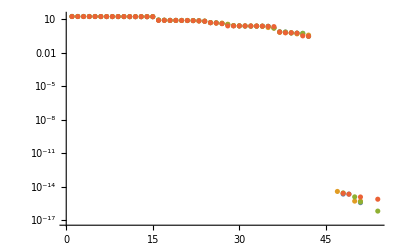

LS it = 17, E = -16.58495526074, Tr[G.S] = 0.0001842176175, Rel.error = -0.01289815272, Trial step = -0.3284204178, Accumulated step = 1.639102089

X Iter=1, Stepsize=1.639102088928223, Energy=-16.58495526073616, Det=0.970456099654228, QDev=0., ObjF=-16.58495526073616, GNorm=0.023728683408815

Old energy: -16.585 Det: 0.960578 Gnorm: 0.0243802

Blocked Hessian

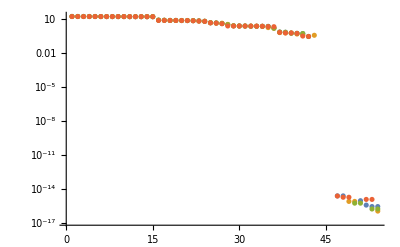

LS it = 15, E = -16.58585492927, Tr[G.S] = 0.000109619606, Rel.error = -0.07392125201, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=2, Stepsize=1.310681671142578, Energy=-16.58585492926728, Det=0.960578091252696, QDev=0., ObjF=-16.58585492926728, GNorm=0.01159906439158974

Old energy: -16.586 Det: 0.96199 Gnorm: 0.0109917

Blocked Hessian

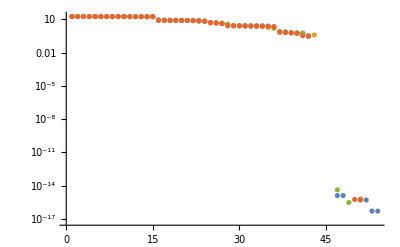

LS it = 15, E = -16.5860194277, Tr[G.S] = 0.00002314199154, Rel.error = -0.08434648923, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=3, Stepsize=1.310681671142578, Energy=-16.58601942770364, Det=0.961990382259624, QDev=0., ObjF=-16.58601942770364, GNorm=0.005757977667459812

Old energy: -16.5861 Det: 0.961732 Gnorm: 0.00630321

Blocked Hessian

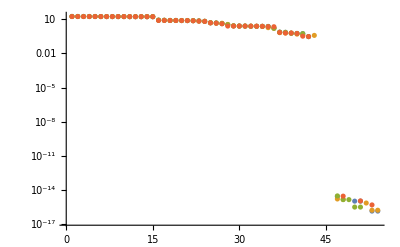

LS it = 15, E = -16.5860631381, Tr[G.S] = 4.546479143×10^-6, Rel.error = -0.06382670569, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=4, Stepsize=1.310681671142578, Energy=-16.58606313809731, Det=0.961731617405728, QDev=0., ObjF=-16.58606313809731, GNorm=0.003030380992950379

Old energy: -16.5862 Det: 0.961715 Gnorm: 0.00233914

Blocked Hessian

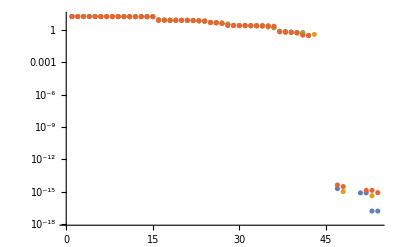

LS it = 15, E = -16.58607621996, Tr[G.S] = 4.683809626×10^-7, Rel.error = -0.02291990859, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=5, Stepsize=1.310681671142578, Energy=-16.58607621995728, Det=0.961715367001846, QDev=0., ObjF=-16.58607621995728, GNorm=0.001628388185444734

Old energy: -16.5862 Det: 0.961656 Gnorm: 0.00231799

Blocked Hessian

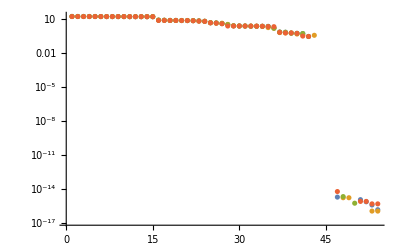

LS it = 15, E = -16.58608031108, Tr[G.S] = -1.226213343×10^-7, Rel.error = 0.0200367637, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=6, Stepsize=1.310681671142578, Energy=-16.58608031108206, Det=0.961656498704879, QDev=0., ObjF=-16.58608031108206, GNorm=0.000876350359437186

Old energy: -16.5862 Det: 0.961649 Gnorm: 0.00194179

Blocked Hessian

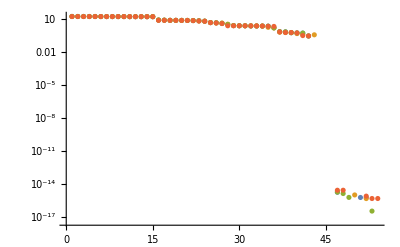

LS it = 15, E = -16.58608166475, Tr[G.S] = -1.473150284×10^-7, Rel.error = 0.07679010219, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=7, Stepsize=1.310681671142578, Energy=-16.58608166475006, Det=0.961649087359503, QDev=0., ObjF=-16.58608166475006, GNorm=0.0005040621913388676

Old energy: -16.5862 Det: 0.961631 Gnorm: 0.00193243

Blocked Hessian

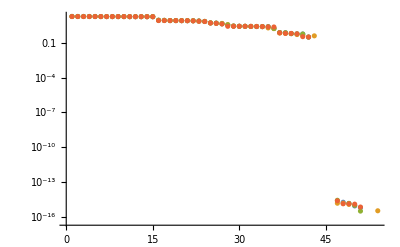

LS it = 19, E = -16.58608210637, Tr[G.S] = -3.419036028×10^-8, Rel.error = 0.0569883938, Trial step = 0.2463153133, Accumulated step = 1.392786776

X Iter=8, Stepsize=1.392786775588989, Energy=-16.58608210636836, Det=0.961631215384787, QDev=0., ObjF=-16.58608210636836, GNorm=0.0002986900631215256

Old energy: -16.5862 Det: 0.961628 Gnorm: 0.00189639

Blocked Hessian

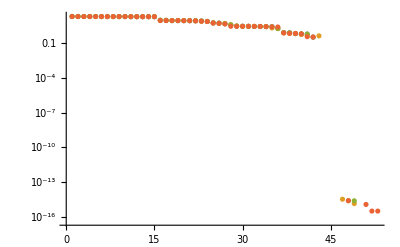

LS it = 15, E = -16.58608225454, Tr[G.S] = -1.252859524×10^-8, Rel.error = 0.05865980378, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=9, Stepsize=1.310681671142578, Energy=-16.58608225454379, Det=0.961627970785337, QDev=0., ObjF=-16.58608225454379, GNorm=0.0001749545946053402

Old energy: -16.5862 Det: 0.961622 Gnorm: 0.00189011

Blocked Hessian

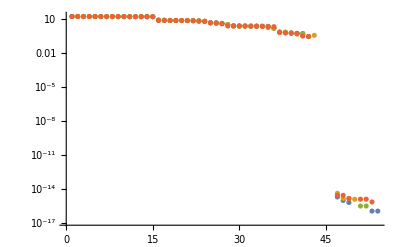

LS it = 15, E = -16.58608229852, Tr[G.S] = -2.908075348×10^-9, Rel.error = 0.04530233194, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=10, Stepsize=1.310681671142578, Energy=-16.5860822985178, Det=0.961621836914697, QDev=0., ObjF=-16.5860822985178, GNorm=0.0001060441266933918

Old energy: -16.5862 Det: 0.961621 Gnorm: 0.00187736

Blocked Hessian

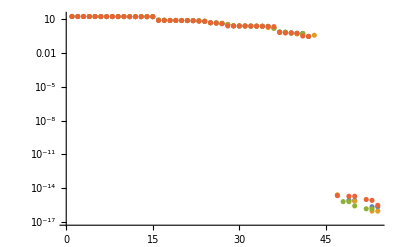

LS it = 15, E = -16.5860823136, Tr[G.S] = -2.020382475×10^-9, Rel.error = 0.09625583157, Trial step = 0.4378938904, Accumulated step = 1.310681671

X Iter=11, Stepsize=1.310681671142578, Energy=-16.58608231359717, Det=0.961620890485029, QDev=0., ObjF=-16.58608231359717, GNorm=0.00006368237638720854

Old energy: -16.5862 Det: 0.961619 Gnorm: 0.00187409

Blocked Hessian

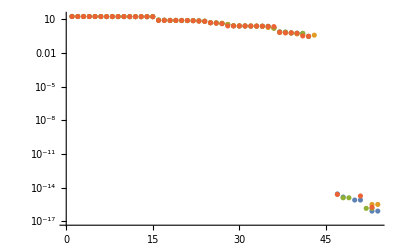

LS it = 16, E = -16.58608231659, Tr[G.S] = -2.569242763×10^-10, Rel.error = 0.04919615717, Trial step = -0.2189469452, Accumulated step = 1.091734726

X Iter=12, Stepsize=1.091734725952148, Energy=-16.58608231658818, Det=0.961618832337497, QDev=0., ObjF=-16.58608231658818, GNorm=0.00004281308577226469

Old energy: -16.5862 Det: 0.961618 Gnorm: 0.00187036

Linear search is not converged after 60 steps. Grad norm along the step is: 0.811467

$Aborted

Characterize final MOs:

|T|=16.04659370873035, E=-16.58616393483947, Det=0.961618498804323, |G|=0.00881834849430484, |q G|=0.001873110040148518, |rq T_n|=0.

Characterize quenched final MOs:

|T|=16.04659370873035, E=-16.58616393483947, Det=0.961618498804323, |G|=0.00881834849430484, |q G|=0.001873110040148518, |rq T_n|=0.

```mathematica
(*Line search methods*)
(*Controls*)
mu0=0.0;(*determinant penalty contribution*)
nu=1.0;(*energy contribution*)
lambda0=0.0;(*localization penalty*)
CG=0; (* conjugated gradient *)
use2der=1;
resetMOs=1; (* start search from the MOs read from the file? if zero, use variables from the prev optimization *)
projHess =0;
taup = 0.001; (* threshold for Hessian projection *)
useNewMethod =1;
newtau = 10; (* threshold for new method *)
NMaxIter=100;
NumGFreq=10000000; (* frequency of computing numerical gradient *)
(*NMaxIterL0=100;*)
ssguess=0.001; (* step size guess *)
(*ssguessL0=0.0001;*)
ssscan=0.0005; (* step size when scanning energy along the line search *)
LSMaxIter=60; (* maximum number of line search iteractions *)
LSscanIter=100; (* maximum number of line search scanner iterations *)
lseps=0.1; (* convergence criterion of the line search *)
maineps=1.0 10^-6; (* main convergence criterion *)
spinfactor=2.0; (* spin factor: 2 for closed shell systems*)
preci1=16; (* number precision when printed *)
minLSPD=1.0 10^-6; (* smallest allowed eigenvalue of the SPD matrix, if the true eigenvalues are smaller the spectrum is shifted up *)
nStepsExponent=20; (* exponent taylor series expansion, max number of terms *)
epsExponent=maineps; (* exponent taylor series expansion, epsilon *)
delta0=0.00001; (* not used *)
nDeltas=2; (* not used *)
SaveHistoryFreq=1;
(*GO!!!*)
If[lambda0≠0.0&&MainVariableType≠1,
Abort[]
];
If[lambda0≠0.0&&AllDOF==0,
Abort[]
];
If[mu0≠0.0&&MainVariableType≠2,
Abort[]
];
If[MainVariableType==2&&use2der≠0&&CG≠0,
Abort[]
];
If[projHess≠0 && useNewMethod≠0,Abort[]];
If[resetMOs≠0,
T0=T0start;
,
T0=MOs;
];
lambda=lambda0;
mu=mu0 spinfactor O1;
GradNormHistory={};
GradPNormHistory = {};
EnergyHistory={};
DetHistory={};
OFHistory={};
PQDHistory={};
GradNormL0History={};
L0NormHistory={};
MONormHistory={};
XNormHistory={};
stepsize=0.0;
(*set initial variables*)

NMaxIterL0=0;
X=T0;
(* START X(+L) ITERATIONS *)
Do[

(*compute MO coefficients*)
MOs=x2mos[MainVariableType,T0Expanded,L0,X,Overlap,OverlapExpanded,OverlapExpandedInv,R0downExpanded,GroupsAOs,GroupsMOs,connect];

MONorms=Diagonal[Transpose[MOs].Overlap.MOs];

(*auxiliary matrices*)
siginv=Inverse[Transpose[MOs].Overlap.MOs];
Proj= MOs.siginv.Transpose[MOs];

(*objective function and its key components*)

{ObjFunction,Gpart1,Gpart2,Qproj,Tbar} = newEnergy[newtau,MOs, H1, connect,GroupsMOs,Overlap, GroupNeighbors, spinfactor,quench,1];
If[iter==0,T0bar = Tbar];
sigbarinv=Inverse[Transpose[Tbar].Overlap.Tbar];
Projbar= Tbar.siginv.Transpose[Tbar];
(*{ObjFunction,Grad1}=newEnergyQ0[MOs,H1,connect,GroupsMOs,Overlap,GroupNeighbors,spinfactor,quench,Qproj0];*)

(*getnewNumGrad[50,H1,Overlap,MOs,spinfactor,delta0,nDeltas,quench,connect,GroupsAOs,GroupsMOs,GroupNeighbors];*)
If[Mod[iter,SaveHistoryFreq]==0,
EnergyHistory=Append[EnergyHistory,ObjFunction];
];


(*grad*)
If[iter≠0,Gprev=Gpart1+Gpart2];
If[useNewMethod==0,
Gfinal=OFGradient[MainVariableType,nu,mu,lambda,MOs,Proj,H1,Overlap,siginv,quench,reversequench0,spinfactor,X,L0,T0Expanded,OverlapExpanded,OverlapHalfExpanded,ZeroExpanded,OverlapExpandedInv,R0downExpanded,R0downHalfExpanded,quenchBlockD,GroupsAOs,GroupsMOs,connect,nStepsExponent,epsExponent,0];
,
(*be sure to change after debug*)
Gfinal = Gpart1;
Gfinalold=OFGradient[MainVariableType,nu,mu,lambda,MOs,Proj,H1,Overlap,siginv,quench,reversequench0,spinfactor,X,L0,T0Expanded,OverlapExpanded,OverlapHalfExpanded,ZeroExpanded,OverlapExpandedInv,R0downExpanded,R0downHalfExpanded,quenchBlockD,GroupsAOs,GroupsMOs,connect,nStepsExponent,epsExponent,0];
];
GNorm=Max[Abs[Gfinal]]; 
GNorm =Max[Abs[Gpart1]];

If[Mod[iter,SaveHistoryFreq]==0,
GradNormHistory=Append[GradNormHistory,GNorm];
];

If[Mod[iter,SaveHistoryFreq]==0,
PrintInfo["X",iter,ObjFunction,SigmaDet,PenaltyQDev,ObjFunction,GNorm,stepsize,preci1];
];
If[useNewMethod≠0,
{oldObjFunction,oldEnergy,SigmaDet,PenaltyQDev}=objFunction[nu,mu,lambda,MOs,Proj,H1,Overlap,siginv,reversequench0,spinfactor];
Print["Old energy: " ,oldEnergy, " Det: " ,SigmaDet, " Gnorm: ", Max[Abs[Gfinalold]]];
];
(*
GfinalQIintersection=ProjectOntoIntersection[1,MOs,Gfinal,Overlap,GroupsMOs,connect,preci1];
GNormQIintersection=Max[Abs[GfinalQIintersection]];
PrintInfo["X",iter,Energy,SigmaDet,PenaltyQDev,ObjFunction,GNormQIintersection,stepsize,preci1];
*)


(* iterations - decision *)
If[GNorm<maineps,
Print["SUCCESS! Iter=",iter];
Break[]
];

(*grad to step*)
If[iter≠0,S1prev=S1];
If[use2der==0 ||( iter>11 && (Mod[iter,11] <10)),
S1=-Gfinal;
,
{S1,HessProj}=grad2step[MainVariableType,projHess,taup,nu,mu,Gfinal,minLSPD,H1,Overlap,Tbar,T0bar,Projbar,sigbarinv,GroupsMOs,GroupsAOs,connect,N1,O1,spinfactor,1,Qproj];
(*use old hessian, just a try*)
(*{S1,HessProj}=grad2step[MainVariableType,projHess,taup,nu,mu,Gfinal,minLSPD,H1,Overlap,MOs,T0,Proj,siginv,GroupsMOs,GroupsAOs,connect,N1,O1,spinfactor,1,Qproj];*)

];


If[CG≠0&&iter≠0,
beta=Tr[Transpose[Gfinal].S1]/Tr[Transpose[Gprev].S1prev];
Print["Beta=",NumberForm[beta,preci1]];
S1=S1+beta S1prev;
];

(*step size*)

(*stepsize=linearsearch[2,MainVariableType,mu,nu,lambda,T0Expanded,L0,X,SL0,S1,quench,reversequench0,Overlap,OverlapExpanded,OverlapHalfExpanded,OverlapExpandedInv,R0downExpanded,R0downHalfExpanded,H1,ZeroExpanded,quenchBlockD,GroupsAOs,GroupsMOs,connect,ssguess,LSMaxIter,lseps,spinfactor,epsExponent];*)
stepsize=newlinearsearch[2,MainVariableType,mu,nu,newtau,GroupNeighbors,lambda,T0Expanded,L0,X,SL0,S1,quench,reversequench0,Overlap,OverlapExpanded,OverlapHalfExpanded,OverlapExpandedInv,R0downExpanded,R0downHalfExpanded,H1,ZeroExpanded,quenchBlockD,GroupsAOs,GroupsMOs,connect,ssguess,LSMaxIter,lseps,spinfactor,epsExponent];

(*ssguess=stepsize;*)

(*Increament*)
X=X+stepsize S1;

,{iter,0,NMaxIter}
];


Print["Characterize final MOs: "];
characterizeMOs[MOs,Overlap,H1,quench0,reversequench0,spinfactor];
Print["Characterize quenched final MOs: "];
characterizeMOs[quench0 MOs,Overlap,H1,quench0,reversequench0,spinfactor];
```

```mathematica
"-15.46177145406041"(*tau 10^-3, converges*)
"-15.46184587782711"(* tau 10^-6 won't converge *)
```

```mathematica
"-15.46188255133968" (* exact *)
```

```mathematica
"-15.4617636399" (* XALMO *)
```

```mathematica
ListLogPlot[{GradPNormHistory}]
```

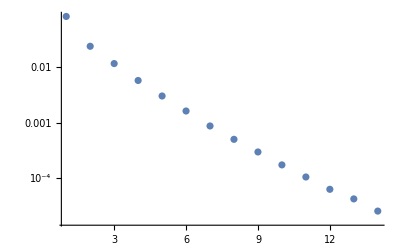

```mathematica
ListLogPlot[GradNormHistory,PlotRange->All]
```

```mathematica
ListLogPlot[GradPNormHistory]
```

```mathematica
ListLogPlot[DetHistory,PlotRange->All]
```

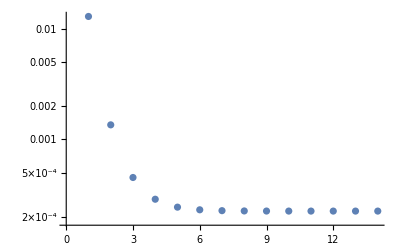

```mathematica
ListLogPlot[EnergyHistory+16.58630726216438]
```

```mathematica
ListLogPlot[PQDHistory]
```

```mathematica
ListLogPlot[OFHistory+16.58630726216438,PlotRange->All]
```

```mathematica
MatrixForm[MOs]
```